The Mathematica^® Journal

# A Flexible Implementation for Support Vector Machines

Roland Nilsson
Johan Björkegren
Jesper Tegnér

Support vector machines (SVMs) are learning algorithms that have many applications in pattern recognition and nonlinear regression. Being very popular, SVM software is available in many versions. Still, existing implementations, usually in low-level languages such as C, are often difficult to understand and adapt to specific research tasks. In this article, we present a compact and yet flexible implementation of SVMs in Mathematica, traditionally named MathSVM. This software is designed to be easy to extend and modify, drawing on the powerful high-level language of Mathematica.

Background

A pattern recognition problem amounts to learning how to discriminate between data points x_i belonging to two classes, defined by class labels y_i∈{+1,-1}, when given only a set of examples (x_i, y_i) from each class. These problems are found in various applications, from automated handwriting recognition to medical expert systems, and pattern recognition or machine learning algorithms are routinely applied to solve them.

It may be helpful for newcomers to relate this to a more familiar problem: standard statistical hypothesis testing for one-dimensional x_i, such as Student’s t-test [Reference, ch. 8], can be viewed as a very simple kind of pattern recognition problem. Here, the hypotheses H_0 and H_1 correspond to classes +1,-1, and the familiar

g(x)={H_(0,) | if x<x̄
H_1, | if x>x̄),

where x̄ is the mean of within-class means,

x̄=1/2(1/l_1∑_(i:y_1=+1) x_i+1/(l_-1)∑_(i:y_1=-1) x_i),

l_c=|{i:y_1=c}| and H_0<H_1, is called the decision rule or sometimes simply the classifier. We say that the decision rule g is induced from data x_i, in this case determined by computing x̄.

However, real pattern recognition problems usually involve high-dimensional data (such as image data) and unknown underlying distributions. In this situation, it is nearly impossible to develop statistical tests like the preceding one. These problems are typically attacked with algorithms, such as artificial neural networks [Reference], decisions trees [Reference, ch. 18], Bayesian models [Reference], and recently SVMs [Reference], to which we will devote the rest of this article. Here we will only consider data that can be represented as vectors x∈R^n; other kinds of information can usually be changed to this form in some appropriate manner.

## Support Vector Machines

SVMs attempt to find a hyperplane Π_(w,b)=w.x+b=0, x∈R^n that separates the data points x_i (meaning that all x_i in a given class are on the same side of the plane), corresponding to a decision rule

g(x)=sign(w.x+b).

In SVM literature, w is often referred to as the weight vector; b is called the bias (a term adopted from neural networks). This idea is not new; it dates back at least to R.A. Fisher and the theory of linear discriminants [Reference]. The novelty of SVMs lies in how this plane is determined: SVMs choose the separating hyperplane w.x+b=0 that is furthest away from the data points x_i, that is, that has maximal margin (Figure 1). The underlying idea is that a hyperplane far from any observed data points should minimize the risk of making wrong decisions when classifying new data. To be precise, in SVMs we maximize the distance to the closest data points. We solve

max_(w,b) (min_i d(Π_(w,b),x_i)),

where d(Π_(w,b),x_i)=|w.x_i+b|/||w|| is the distance between data point i and the plane Π_w, subject to the constraint that this plane still separates the classes. The plane Π_w that solves (1) is called the optimal separating hyperplane and is unique [Reference]. MathSVM provides algorithms for determining this plane from data.

Figure NumberedFigure. Two-class data (black and grey dots), their optimal separating hyperplane (continuous line), and support vectors (circled in blue). This is an example output of the SVMPlot function in MathSVM. The width of the “corridor” defined by the two dotted lines connecting the support vectors is the margin of the optimal separating hyperplane.

## Solving the Optimization Problem

The Primal Problem

It turns out that the optimal separating hyperplane solving (1) can be found as the solution to the equivalent optimization problem

min_(w,b) 1/2||w(||)^2
subject to y_i(w^T x_i+b)≥1,

referred to as the primal problem. Typically, only a small subset of the data points will attain equality in the constraint; these are termed support vectors since they are “supporting” (constraining) the hyperplane (Figure 1). In fact, the solution (w,b) depends only on these specific points. Therefore, the method also is a scheme for data compression, in the sense that the support vectors contain all the information necessary to derive the decision rule.

### The Dual Problem

For reasons that will become clear later, w often has very high dimension, which makes the primal problem (2) intractable. Therefore, we attack (2) indirectly, by solving the dual problem

min_α α^T Qα-α
subject to α_i≥0, y^T α=0,

where Q=(q_(i j))=(y_i y_j x_j x_i). This is a quadratic programming (QP) problem, which has a unique solution whenever Q is positive semidefinite (as is the case here). It is solved numerically in MathSVM by the function QPSolve. (At this point we need to load the MathSVM package; see Additional Material.)

```mathematica
SetDirectory["E:\\work\\thesis\\kaiTi\\nb"];
<<MathSVM`
(*<<Statistics`NormalDistribution`*)
ResetDirectory[];
```

```mathematica
?QPSolve
```

QPSolve[Q,p,a,b,c,y,τ] solves the quadratic programming problem min α.Q.α+p.α, subject to a≤α≤b and y.α=c. QPSolve uses the GSMO algorithm described by Keerthi et al. τ is a solution tolerance parameter (0.01 or so is usually good enough for SVMs). Q must be a positive semidefinite matrix to guarantee convergence.

The variable α has dim α=l, the number of data points, so the matrix Q has l^2 elements, which may be quite large for large problems. Therefore, QPSolve employs a divide-and-conquer approach [Reference] that allows for solving (3) efficiently without storing the full matrix Q in memory.

Having solved the dual problem for α using QPSolve, we obtain the optimal weight vector w and bias term b, that is, the solution to the primal problem (2), using the identities

w=∑_i α_i y_i x_i

b=-1/2(w^T x_++w^T x_-),

where in (5) x_+,x_- are any two support vectors belonging to class +1 and -1, respectively (there always exist at least two such support vectors) [Reference].

### A Simple SVM Example

Enough theory—let us generate some data and solve a simple SVM problem using MathSVM.

```mathematica
len=20;
X=Join[
RandomArray[NormalDistribution[-2,1],{len/2,2}],
RandomArray[NormalDistribution[2,1],{len/2,2}]];
y=Join[Table[1,{len/2}],Table[-1,{len/2}]];
```

For this elementary problem, we use the simple SVM formulation (2) provided in MathSVM by the SeparableSVM function.

```mathematica
τ=0.01;
α=SeparableSVM[X,y,τ]
```

{0,0.286301,0,0,0.217651,0,0,0,0,0,0.503951,0,0,0,0,0,0,0,0,0}

The returned vector α is the solution found by QPSolve for the dual formulation (3) of the SVM problem we just constructed. For this specific problem, the dual formulation used is exactly that described by (3), that is

Q | = | (q_(i j))=(y_i y_j x_j x_i)
p | = | (-1,… ,-1)
a | = | (0,… ,0), b=(0,… ,0)
c | = | 0

The support vectors are immediately identifiable as the nonzero α_i. (4) and (5) are implemented as

```mathematica
WeightVector[α,X,y]
```

{-0.728021,-0.688953}

```mathematica
Bias[α,X,y]
```

0.327599

A plot similar to Figure 1 is produced by the SVMPlot function. As in Figure 1, the solid line marks the optimal hyperplane, and dotted lines mark the width of the corridor that joins support vectors (highlighted in blue).

DisplayTogether::obslt: The DisplayTogether and DisplayTogetherArray functions are obsolete in Version 6. GraphicsArray and Show may be used directly in the same role.

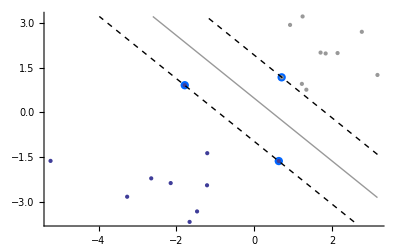

```mathematica
SVMPlot[α,X,y]
```

### Nonseparable Data

Often the assumption of separable training data is not reasonable (it may fail even for the preceding simple example). In such cases, NonseparableSVM should be used. This SVM variant takes a parameter C that determines how hard points violating the constraint in (2) should be penalized. This parameter appears in the objective function of the primal problem, which now is formulated as [Reference]

min_(w,b,ξ) 1/2||w.w||+C∑_i ξ_i
subject to y_i(x_i.w+b)≥1-ξ_i, ξ_i≥0.

Large C means high penalty, and in the limit C→∞ we obtain the separable case.

```mathematica
τ=0.01;
α=NonseparableSVM[X,y,0.5,τ]
```

{0,0.284056,0,0,0.215944,0,0,0,0,0,0.5,0,0,0,0,0,0,0,0,0}

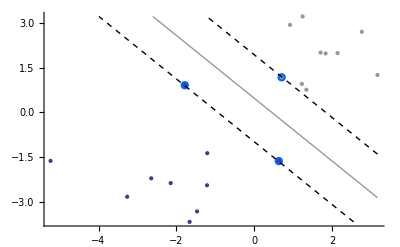

```mathematica
SVMPlot[α,X,y]
```

### Getting QP Formulations

Sometimes it is interesting to examine what the QP problem looks like for a given SVM formulation. Using the option FormulationOnly, we can inspect the various parameters instead of actually solving the QP. This can, for example, be used to study expressions analytically.

```mathematica
Clear[X,y,α,len]
```

```mathematica
τ=0.01;
NonseparableSVM[Array[x,{2,2}],Array[y,{2}],C,τ,FormulationOnly->True]
```

Matrix[{{{(x[1,1]^2+x[1,2]^2) y[1]^2,(x[1,1] x[2,1]+x[1,2] x[2,2]) y[1] y[2]},{(x[1,1] x[2,1]+x[1,2] x[2,2]) y[1] y[2],(x[2,1]^2+x[2,2]^2) y[2]^2}},{-1,-1},{0,0},{C,C},0,{y[1],y[2]},0.01}]

The parameters are given in the order corresponding to the arguments of QPSolve.

## Feature Space and Kernels

In all of the preceding examples, the separating surface is assumed to be linear (a hyperplane). This is often a serious limitation, as many pattern recognition problems are inherently nonlinear in the input data and require nonlinear separating surfaces. To overcome this obstacle, for each specific problem we devise some appropriate transformation ϕ(x) from input space X (the domain of the original data) to a feature space H. The function ϕ is chosen so that a hyperplane in H corresponds to some desirable class of surfaces in X. (Choosing this function for a specific problem is something of an art, but we can always try a few different ϕ known to have been successful in similar problems and simply hope for the best.)

As an example, consider a second-degree polynomial surface in R^2, described by w_1+w_2 x_1+w_3 x_2+w_4 x_1^2+w_5 x_1 x_2+w_6 x_2^2=0. We may represent such a surface by choosing a mapping X→H as

ϕ(x_1,x_2)=(1,x_(1,)x_2,x_1^2,x_1 x_2,x_2 x_(1,)x_2^2)

and forming a hyperplane in H defined by w.z+b=0, where z=ϕ(x). If we now solve the problem in the new variables z, we obtain a wide-margin hyperplane in H corresponding to a second-degree surface in X.

The problem with this approach is that nonlinear ϕ-transformations may have huge dimensions. Even for the simple quadratic surface considered here, we obtain dim H= 1+n+n^2 when dim X=n. For increasing polynomial degree, this number grows quickly, and there are even nonlinear functions that result in infinite-dimensional H. This is why we do not solve the primal problem (2) directly: w may not be a finite vector, but α always is.

This problem is elegantly solved by kernels. It turns out that there are many functions ϕ for which we can compute scalar products ϕ(x).ϕ(y) in H implicitly, without actually calculating ϕ. And in fact, this is all we need for solving the SVM formulation (1). Thus we define the kernel function as

K(x,y)=ϕ(x).ϕ(y)

In the case of example (6), it turns out that K(x,y)=ϕ(x).ϕ(y)=(1+x.y)^2, which is why we chose that specific form of ϕ (explaining the two separate terms x_1 x_2 and x_2 x_1). It is not difficult to prove that this result holds for any polynomial degree d; therefore, using the polynomial kernel

K_d(x,y)=(1+x.y)^d

we can obtain any polynomial separating surfaces.

### A Nonlinear Example: Using Kernels

Let us see how kernels are handled in MathSVM to solve nonlinear problems. The second-degree kernel in (6) is provided by

```mathematica
PolynomialKernel[x,y,2]
```

(1+x.y)^2

Here is some data a linear classifier cannot possibly cope with.

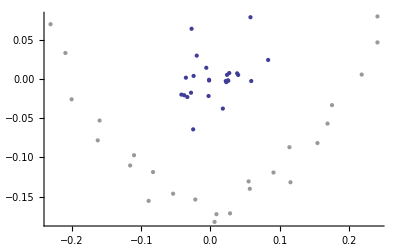

```mathematica
len=50;
X=Join[
RandomArray[NormalDistribution[0,0.03],{len/2,2}],
Table[
{Random[NormalDistribution[i/len-1/4,0.01]],Random[NormalDistribution[(2i/len-1/2)^2-1/6,0.01]]},
{i,len/2}]];
y=Join[Table[1,{len/2}],Table[-1,{len/2}]];
SVMDataPlot[X,y,PlotRange->All]
```

Let us solve this problem using the polynomial kernel. This is done as before, by supplying the desired kernel (which can be any function accepting two arguments) using the KernelFunction option.

```mathematica
τ=0.01;
pk=PolynomialKernel[#1,#2,2]&;
α=SeparableSVM[X,y,τ,KernelFunction->pk]
```

{0,0,0,0,0,0,0,0,0,5408.67,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,808.887,0,0,0,2311.38,0,0,0,0,0,0,0,0,0,0,0,0,2065.46,0,0,0,0,0,222.949}

When visualizing the results, SVMPlot can use the kernel functions to draw any nonlinear decision curves.

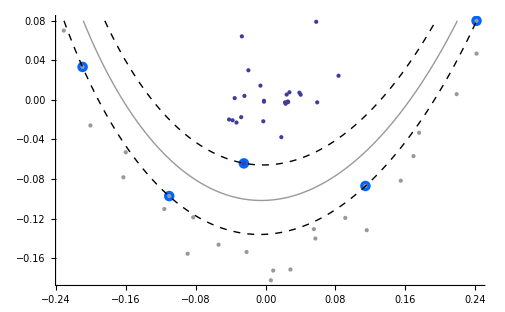

```mathematica
SVMPlot[α,X,y,KernelFunction->pk]
```

```mathematica
Clear[len,X,y,α,pk]
```

### High-Dimensional Input Spaces

An interesting consequence of the kernel idea is that the dimensionality of the input space X does not matter for the time-complexity of the SVM algorithm. Since the solution is computed using only dot products between samples (in input space or some feature space), high-dimensional problems are solved equally fast (not considering the time used to precalculate the kernel matrix Q, which is usually not noticeable). As an example of this, consider a problem with dimension n=1000.

```mathematica
len=20;n=1000;
X=Join[
RandomArray[NormalDistribution[-2,1],{len/2,n}],
RandomArray[NormalDistribution[2,1],{len/2,n}]];
y=Join[Table[1,{len/2}],Table[-1,{len/2}]];
```

The kernel matrix is still just l×l.

```mathematica
KernelMatrix[IdentityKernel,X]//Dimensions
```

{20,20}

The SVM algorithm is still fast, although the problem is much harder due to extremely low sample density, which is reflected by more support vectors (the nonzero α_i).

```mathematica
τ=0.01;
(α=SeparableSVM[X,y,τ])//Timing
```

{0.063,{1.21109×10^-6,0,0.0000129387,0.0000203788,0,0.0000207636,0.0000169975,0,0.0000178615,0.0000355008,0.0000340863,0.0000177229,0.0000183991,3.91484×10^-6,0.0000101495,0.0000124396,0.0000147123,0,0.0000142275,0}}

The solution in this case may be viewed using the projection of data onto the weight vector w. The separation looks almost perfect, although there will be problems with overfitting (the solution may not work well when applied to new, unseen examples x). However, this problem is outside the scope of the present article.

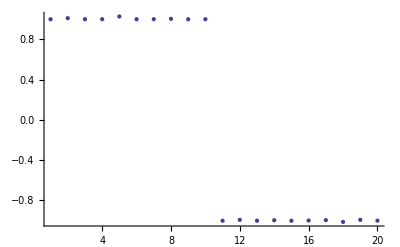

```mathematica
ListPlot[X.WeightVector[α,X,y]]
```

## Regression Analysis with SVMs

So far we have considered SVMs as a tool for pattern recognition only. It is also possible to use the SVM framework for regression problems. Consider a function y=f(x) to be approximated; for example, a quadratic.

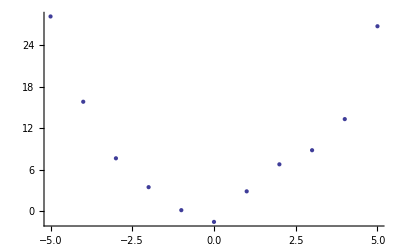

```mathematica
X=Range[-5,5];len=Length[X];
y=Map[#^2+Random[NormalDistribution[0,2]]&,X];
ListPlot[Thread[{X,y}]]
```

We can adapt the SVM method to the regression setting by using a ϵ-insensitive loss function

L_ϵ(f(x),g(x))={0, ||f(x)-g(x)||<ϵ
||f(x)-g(x)||-ϵ, otherwise

where g(x) is the SVM approximation to the regression function f(x). This loss function determines how much a deviation from the true f(x) is penalized; for deviations less than ϵ, no penalty is incurred. Here is what the loss function looks like.

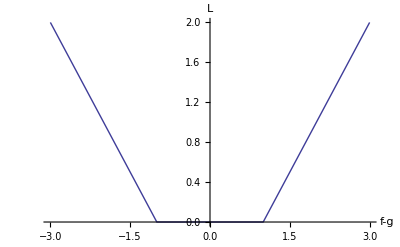

```mathematica
Plot[If[Abs[x]<1,0,Abs[x]-1],{x,-3,3},AxesLabel->{"f-g","L"}]
```

Using this idea, the regression problem is transformed to a classification problem: any x such that L_ϵ(f(x),g(x))=0 may be considered “correctly classified.” MathSVM solves such problems using the RegressionSVM function, parameterized by ϵ and a penalty constant C. Here we again try a polynomial kernel.

```mathematica
pk=PolynomialKernel[#1,#2,2]&;
ϵ=3;c=0.5;
τ=0.01;
α=RegressionSVM[X,y,c,ϵ,τ,KernelFunction->pk]
```

{0,0,0,0,0,0.0365316,0,0,0,0,0,0.025306,0,0,0,0,0,0,0,0,0,0.0112256}

The function RegressionSVMPlot provides convenient plotting of the resulting regression function. As with SVMPlot, the kernel type used is supplied as a parameter. Note how support vectors in this case are chosen as the data points that are furthest away from the regression line.

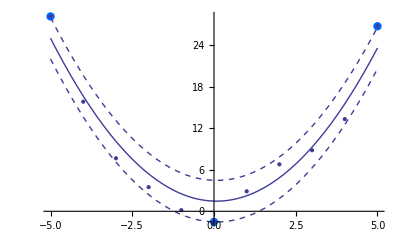

```mathematica
RegressionSVMPlot[α,X,y,ϵ,KernelFunction->pk]
```

```mathematica
RegressionBias[α,X,y,ϵ,KernelFunction->pk]
```

1.47221

We can, of course, also obtain the analytical expression of the estimated regression function.

```mathematica
RegressionFunction[α,X,y,ϵ,x,KernelFunction->pk]
```

1.43568+0.025306 (1-5 x)^2+0.0112256 (1+5 x)^2

```mathematica
Clear[α,X,y,pk,ϵ,c,len]
```

### Two-Dimensional Example

We can use SVM regression with domains of any dimension (that is the main advantage). Here is a simple two-dimensional example.

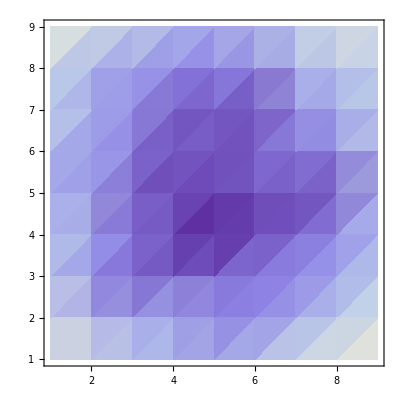

```mathematica
X=Table[{i,j},{i,-4,4},{j,-4,4}];
y=Map[(((#⟦1⟧)^2+(#⟦2⟧)^2)/5+Random[NormalDistribution[0,0.5]])&,X,{2}];
ListDensityPlot[y]
X=Flatten[X,1];y=Flatten[y];
```

```mathematica
pk=PolynomialKernel[#1,#2,2]&;
ϵ=3;c=0.5;
τ=0.01;
α=RegressionSVM[X,y,c,ϵ,τ,KernelFunction->pk]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0020686,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000727036,0,0,0,0,0,0,0,0.00134156,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Here is the regression function.

```mathematica
rf=RegressionFunction[α,X,y,ϵ,{i,j},KernelFunction->pk]
```

2.13762-0.0020686 (1-i)^2+0.000727036 (1-4 i-4 j)^2+0.00134156 (1-4 i+4 j)^2

There are no specialized 3D plots for regression in the MathSVM package. Here is the usual Plot3D visualization.

```mathematica
Plot3D[rf,{i,-4,4},{j,-4,4}]
```

-Graphics3D-

## Conclusion

In this article, we have demonstrated the utility of the MathSVM package for solving pattern recognition and regression problems. This is an area of very active research and these algorithms are evolving quickly. In a rapidly moving field such as this, it is important to have a clear, well documented, high-level approach to implementation to minimize confusion. Mathematica provides an excellent solution here, due to its high-level programming language and symbolic capabilities.

MathSVM is currently 100% native Mathematica code, written with the emphasis on clarity. This does incur penalties in terms of computational speed. Some parts of the QP algorithm are therefore being ported to Java at this time to improve performance. This should not impair the clarity of the software in any way, since the QPSolve function is easy separable from the other parts of MathSVM in a “black box” fashion.

The MathSVM software is still in its infancy and will no doubt expand rapidly, as our group is currently involved in many projects in pattern recognition and high-dimensional data analysis in general, as well as in a biomedical context. We hope that this contribution will initiate other efforts to bring understandable implementations of machine learning algorithms to the Mathematica community.

## References

[Reference]  G. Casella and R. L. Berger, Statistical Inference, 2nd ed., Belmont, CA: Duxbury Press, 2002.

[Reference]  S. Haykin, Neural Networks: A Comprehensive Foundation, 2nd ed., Englewood Cliffs, NJ: Prentice Hall, 1999.

[Reference]  S. Russell and P. Norvig, Artificial Intelligence: A Modern Approach, Englewood Cliffs, NJ: Prentice Hall, 1995.

[Reference]  N. Friedman, “Inferring Cellular Networks Using Probabilistic Graphical Models,” Science, 303, 2004 pp. 799–805.

[Reference]  V. N. Vapnik, Statistical Learning Theory, New York: John Wiley & Sons, 1998.

[Reference]  R. A. Fisher, “The Statistical Utilization of Multiple Measurements,” Annals of Eugenics, 8, 1938 pp. 376–386.

[Reference]  S. S. Keerthi and E. G. Gilbert, “Convergence of a Generalized SMO Algorithm for SVM Classifier Design,” Machine Learning, 46, 2002 pp. 351–360.

## Additional Material

MathSVM.nb
MathSVM.m

Available at www.mathematica-journal.com/issue/v10i1/download.

About the Authors

Roland Nilsson is a graduate student at Linköping University working with machine learning algorithms in analysis of high-dimensional biomedical data.

Johan Björkegren is an associate professor in molecular medicine at Karolinska Institutet, Sweden, and cofounder of Clinical Gene Networks, a biotechnology company involved in system-level analysis of biomedical data in cardiovascular disease.

Jesper Tegnér is a professor of computational biology at Linköping University, Sweden, and cofounder of Clinical Gene Networks.

Roland Nilsson
Computational Biology 
Linköping University
SE-58183 Linköping, Sweden
rolle@ifm.liu.se

Johan Björkegren
Center for Genomics and Bioinformatics 
Karolinska Institutet
SE-17177 Stockholm, Sweden
johan.bjorkegren@ks.se

Jesper Tegnér
Computational Biology 
Linköping University
SE-58183 Linköping, Sweden
jespert@ifm.liu.se